Are we ready to transfer optical light to gamma-rays?

M. Vranic, T. Grismayer, S. Meuren, R. A. Fonseca, and L. O. Silva, Phys. Plasmas 26, 053103 (2019)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Figure 2

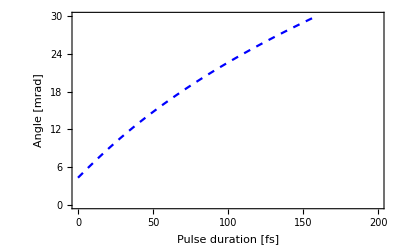

```mathematica
Clear[γF,σF,a0,θF,I22,Ι,γ0,k,θ];

(* eq 2: CRR final "average" electron energy *)
γF=γ0/(1+k γ0);

(* eq 3: CRR factor *)
k=3.2 10^-5 I22 τ0(1-Cos[θ])^2;

(* eq 6: estimated final electron energy spread *)
σF=((1.5 10^-4 I22^(1/2)γ0^3)/((1+6.1 10^-5 γ0 I22 τ0)^3))^(1/2);

(* eq7: estimated final electron angular spread, see [Vranic2016NJP]*)
θF=Sqrt[2/π] a0/γF^2 σF;

(* conversion between intensity and a0 *)
I22 = Ι 10^-22;
Ι=10^(+18)(a0/(0.855/√2))^2;

(* parameters *)
θ=π;(*[] collision angle, counter-propagating *)
γ0=0.85/(0.511 10^-3);(*[] initial electron energy *)
a0=27;(*[] laser a0 *)

Plot[10^3 θF,{τ0,0,200},Frame->True,FrameLabel->{"Pulse duration [fs]","Angle [mrad]"},PlotRange->{0,30},PlotStyle->{{Blue,Dashed}}]
```

## Figure 3

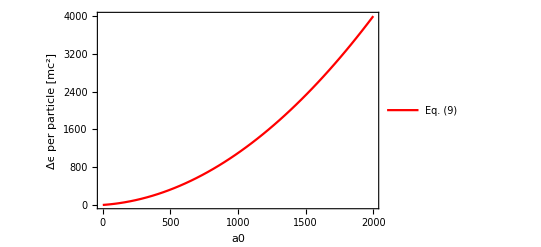

```mathematica
Clear[a0,Δγ]
Δγ=9 10^-4 a0^2+0.2 a0;
Plot[Δγ,{a0,0,2000},FrameLabel->{"a0","Δϵ per particle [mc^2]"},Frame->True,PlotStyle->{Red},PlotLegends->{"Eq. (9)"}]
```

## Figure 5

(0.0333333 a0 nc)/(0.2+0.0009 a0)

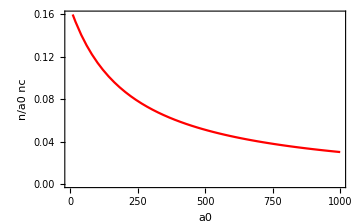

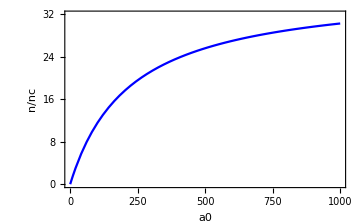

```mathematica
Clear[Δϵϵ,a0,n,nc]
(*n=160nc;*)

(* eq 11 *)
Δϵϵ=(3(9 10^-4 a0+0.2))/a0(n/nc);
(* 10% absorption *)
sol=Solve[Δϵϵ==0.1,n][[1,1,2]]

Plot[{sol/a0/.{nc->1,n->160}},{a0,0,1000},Frame->True,FrameLabel->{"a0","n/a0 nc"},PlotStyle->Red,ImageSize->Medium,PlotLegends->Automatic,PlotRange->{0,0.16}]

Plot[{sol/.{nc->1,n->160}},{a0,0,1000},Frame->True,FrameLabel->{"a0","n/nc"},PlotStyle->Blue,ImageSize->Medium,PlotLegends->Automatic,PlotRange->{0,32}]
```

## Figure 6

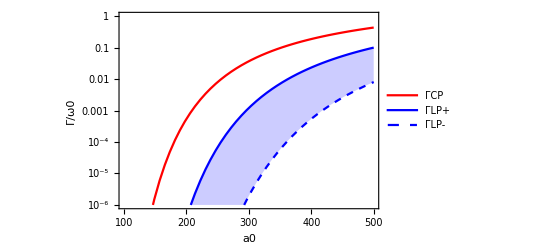

```mathematica
Clear[a0,ΓCP,ΓLPp,ΓLpm,ω0,aS,λ]

(* eq 12 *)
ΓCP = ω0 2.6 10^-3 a0 Exp[-(2aS)/(3 a0^2)];

(* eq 13 *)
ΓLPp = ω0 1.8 10^-3 a0 Exp[-(4aS)/(3 a0^2)];

(* eq 14 *)
ΓLPm = ω0 1.3 10^-3 a0 Exp[-(8aS)/(3 a0^2)];

ω0=1;(*[ω0] for plotting purposes*)
λ=1;(*[μm]*)
aS=4.12 10^5 λ;(*[]*)

LogPlot[{ΓCP,ΓLPp,ΓLPm},{a0,100,500},PlotRange->{10^-6,10^0},Frame->True,FrameLabel->{"a0","Γ/ω0"},PlotLegends->{"ΓCP","ΓLP+","ΓLP-"},PlotStyle->{Red,{Blue},{Blue,Dashed}},Filling->{2->{3}}]
```